## Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

Eventually, these functions may want to use the Notation` package to actually make the subscripted letters have downvalues. For now, I’m just being careful.

```mathematica
Clear@ClearSubscripts
ClearSubscripts[top_]:=(
(Unset[Evaluate[#[[1]]]];Evaluate[#[[1]]])&/@Select[DownValues[Subscript],#[[1,1,1]]==top&]
)
Clear@unknownArray
unknownArray[top_,dim_/;NumberQ[dim]]:=(
Table[Subscript[top, i],{i,dim}]
)
unknownArray[top_,{dim1_/;NumberQ[dim1],dim2_/;NumberQ[dim2]}]:=(
Table[Subscript[top, i,j],{i,dim1},{j,dim2}]
)
```

## Investment

### Pt 1

```mathematica
A=({{"Chris", 100, 100, 100}, {"Rebecca", 100, 200, 200}, {"Siddhartan", 50, 50, 200}});
stocks={1,Quantity["100.00", "USDollars"],Quantity["50.00", "USDollars"],Quantity["20.00", "USDollars"]};
```

```mathematica
A.stocks//MatrixForm
A.stocks/.x_+y_:>{x,y}//MatrixForm
```

(Chris+17 000.00 $
Rebecca+24 000.00 $
Siddhartan+11 500.00 $)

(Chris | 17 000.00 $
Rebecca | 24 000.00 $
Siddhartan | 11 500.00 $)

### Pt 2

```mathematica
ClearSubscripts[x];
unknown=unknownArray[x,{3,3}];
money=({{1500, 1600, 1400}, {2600, 2810, 2550}, {950, 1020, 1000}});
prices=({{100, 110, 100}, {50, 50, 40}, {20, 22, 30}});
eqn=unknown.prices==money;
```

```mathematica
Solve[eqn,Variables[eq]][[1]]
(unknown/.%)//MatrixForm
```

{x_(1,1)→10,x_(1,2)→10,x_(1,3)→0,x_(2,1)→20,x_(2,2)→10,x_(2,3)→5,x_(3,1)→5,x_(3,2)→5,x_(3,3)→10}

(10 | 10 | 0
20 | 10 | 5
5 | 5 | 10)

## Physics

Helper function: 2D scalar cross product

```mathematica
Clear@cross;
cross[a_,b_]:=(Append[a,0]×Append[b,0])[[3]]
```

Step 1: calculate the equivalent force (and location) of the lift.

```mathematica
Clear@liftforce;
liftforce[x_]:=200 Sqrt[1-x^2/17]
intercept=x/.Solve[{liftforce[x]==0,x>0},x][[1]];
{liftmag,liftpos}=Integrate[{1,x}*liftforce[x],{x,0,intercept}]/.{t_,x_}:>{t,x/t}
```

{50 √17 π,(4 √17)/(3 π)}

Step 2: Define the forces (and associated radii) for each force and moment.
Force 1 is between the wing and the fuselage
Force 2 is between the strut and wing
Force 3 is lift

```mathematica
F1=unknownArray[f1,2];
F2=unknownArray[f2,2];
F3={0,liftmag};
r1={0,0};
r2={2,0};
r3={liftpos,0};
```

Setup motion equations

```mathematica
forceeqn=Thread[F1+F2+F3=={0,0}];
momenteqn=m+cross[r1,F1]+cross[r2,F2]+cross[r3,F3]==0;
```

Solution strategy 1: use Solve[]

```mathematica
Solve[{forceeqn,momenteqn},Variables@{forceeqn,momenteqn}]
```

{{f1_2→m/2-50/3 (-34+3 √17 π),f2_1→-f1_1,f2_2→-1700/3-m/2}}

Solution strategy 2: use Reduce[]

```mathematica
Reduce[{forceeqn,momenteqn},Variables@{forceeqn,momenteqn}]
```

f1_1==-f2_1&&f1_2==-50 √17 π-f2_2&&m==-3400/3-2 f2_2

Solution strategy 3: use a matrix

```mathematica
vars={Subscript[f1, 1],Subscript[f2, 1],Subscript[f1, 2],Subscript[f2, 2],m};
```

```mathematica
{b,a}=Normal@CoefficientArrays[Flatten@{forceeqn,momenteqn},vars];
HoldForm@A==(a//MatrixForm)
HoldForm@b==(b//MatrixForm)
```

A==(1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 2 | 1)

b==(0
50 √17 π
3400/3)

Now, the solution has been reduced to the form [A.vars=b].

```mathematica
Solve[a.vars==b,vars]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{f2_1→-f1_1,f2_2→50 √17 π-f1_2,m→-100/3 (-34+3 √17 π)+2 f1_2}}

## Electronics

I' ll come back to this after hearing the in class explanation. It is probably useful, so I' m sorry I didn't solve it.

## Types of Solutions

### Solving with Elimination

This function carries out rotely the elimination algorithm for 2-d equation solvers given. Notice that I use x and y instead of x_1 and x_2, simply for brevity.

```mathematica
Clear@elim2
elim2[eq1_,eq2_]:=Module[{soleq1,soleq2,xval,yval},
soleq1=Solve[eq1,{x}][[1]];
soleq2=eq2/.soleq1;
yval=y/.Solve[soleq2,y][[1]];
xval=soleq1[[1,2]]/.y->yval;
{xval,yval}
]
```

Note that the solution given in the BB is (1
3/2), an erroneous typo.

```mathematica
elim2[2x+3y==6,4x+9y==15]//MatrixForm
```

(3/2
1)

This equation has infinitely many solutions:

```mathematica
elim2[x+2y==1,2x+4y==2]//MatrixForm
```

(1-2 y
y)

The result here states that as long as y==y (trivially true) and x==1-2y, the equations are satisfied.

This equation has no solutions.

```mathematica
elim2[x+2y==1,2x+4y==1]//MatrixForm
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(1-2 (y/.{}⟦1⟧)
y/.{}⟦1⟧)

As expected, warnings are thrown and a nonsensical result is returned. In particular, the first solution to an equation with no solutions doesn’t exist. I’d like the error to be more intuitive, but this works.

### Solving for h, k

```mathematica
elim2[x+h y==1,2x+3y==k]//MatrixForm
```

(1-(h (2-k))/(-3+2 h)
(2-k)/(-3+2 h))

Interpreting this result is a little hoakey. In particular, it is clear that something interesting happens when h=3/2, but it takes some thought to realize that the result is no solution because n/0 is undefined for nonzero n. On the other hand, if h=3/2&&k=2, then the y value is 0/0, which allows for infinitely many solutions.

Amazingly, this code was written once, then applied to all of the cases without needing to be tested, altered, or generalized. I think that’s interesting.

### Three variables

This code is a pretty simple extension of the stuff above, but demonstrates the added complexity from solving higher-order equations using elimination.

```mathematica
Clear@elim3
elim3[eq1_,eq2_,eq3_]:=Module[{},
soleq1=Solve[eq1,x][[1]];
soleq2=Solve[eq2/.soleq1,y][[1]];
zval=z/.Solve[eq3/.Join[soleq1,soleq2],z][[1]];
yval=soleq2[[1,2]]/.z->zval;
xval=soleq1[[1,2]]/.{z->zval,y->yval};
{xval,yval,zval}
]
```

When I fed in the equations in the given order, this code broke. I suspect that this is the primary reason elimination isn’t a good way for computers to solve these things.

```mathematica
elim3[x+y+z==6,x-2z==4,y+z==4]
```

{2,5,-1}

Result: 1 solution

```mathematica
elim3[x+y+z==-6,2x+y-z==18,y-2z==4]
```

{52/5,-48/5,-34/5}

Result : 1 solution

```mathematica
elim3[2x+y-z==10,x+y+z==6,y+z==2]
```

{4,2,0}

Result : 1 solution

Ummm. Those results are not right. I think I’ve hit the limits of reasonable programmability of elimination, and while I could certainly work it out by hand, cursory visual inspection reveals the answers are (One, none, many). I’ll come back and fix this if I have time.
Lesson learned: Don’t do elimination by computer!

## Gauss-Jordan Elimination

I’ve done the by-hand part of this far too many times before for my Linear Algebra class, and that was valuable. Doing it again now wouldn’t be, so I’m not going to.

```mathematica
aug=({{1, 1, 1, 6}, {0, 1, 1, 2}, {1, 0, -2, 4}});
RowReduce[aug]//MatrixForm
```

(1 | 0 | 0 | 4
0 | 1 | 0 | 2
0 | 0 | 1 | 0)

Result: Single solution

```mathematica
aug=({{1, 1, 1, -6}, {2, 1, -1, 18}, {1, 0, -2, 4}});
RowReduce[aug]//MatrixForm
```

(1 | 0 | -2 | 0
0 | 1 | 3 | 0
0 | 0 | 0 | 1)

Result: No solutions

```mathematica
aug=({{1, 1, 1, 6}, {2, 1, -1, 10}, {1, 0, -2, 4}});
RowReduce[aug]//MatrixForm
```

(1 | 0 | -2 | 4
0 | 1 | 3 | 2
0 | 0 | 0 | 0)

Result: Infinitely many solutions

I realize that this is the fuller form, but don’t see much point in stopping before achieving  the leading 1’s coefficient.

## LU Decomposition

The LUDecomposition command returns the results in an annoying flattened format. This fixes that. Warning: for convenience, it drops the permutation matrix, causing potentially incorrect results.

```mathematica
Clear[LU]
LU[mat_]:=Module[{lu,p,c,l,u},
{lu,p,c}=LUDecomposition[mat];
l=lu SparseArray[{i_,j_}/;j<i->1,Dimensions@mat]+IdentityMatrix[Length@mat];
u=UpperTriangularize[lu];
{l,u}
]
```

```mathematica
mat=({{1, 1, 1}, {0, 1, 1}, {1, 0, -2}});
Grid[{{"L","U"},MatrixForm/@LU[mat]}]
```

L | U
(1 | 0 | 0
0 | 1 | 0
1 | -1 | 1) | (1 | 1 | 1
0 | 1 | 1
0 | 0 | -2)

My manual calculation agrees.

This next problem encapsulates both the second and third examples (they’re identical).

```mathematica
mat=({{1, 1, 1}, {2, 1, -1}, {1, 0, -2}});
Grid[{{"L","U"},MatrixForm/@LU[mat]}]
```

LUDecomposition::sing: Matrix {{1,1,1},{2,1,-1},{1,0,-2}} is singular.

L | U
(1 | 0 | 0
2 | 1 | 0
1 | 1 | 1) | (1 | 1 | 1
0 | -1 | -3
0 | 0 | 0)

My manual calculation agrees. The singular nature of the matrix does not prevent successful calculation.

## Determinant

### 1

```mathematica
mat=({{1, 1, 1}, {0, 1, 1}, {1, 0, -2}});
Grid[{{"L","U"},MatrixForm/@LU[mat]}]
Print["Manual result: -2"]
Det[mat]
```

L | U
(1 | 0 | 0
0 | 1 | 0
1 | -1 | 1) | (1 | 1 | 1
0 | 1 | 1
0 | 0 | -2)

Manual result: -2

-2

### 2/3

```mathematica
mat=({{1, 1, 1}, {2, 1, -1}, {1, 0, -2}});
Grid[{{"L","U"},MatrixForm/@LU[mat]}]
Print["Manual result: 0"]
Det[mat]
```

LUDecomposition::sing: Matrix {{1,1,1},{2,1,-1},{1,0,-2}} is singular.

L | U
(1 | 0 | 0
2 | 1 | 0
1 | 1 | 1) | (1 | 1 | 1
0 | -1 | -3
0 | 0 | 0)

Manual result: 0

0

## Inverse

```mathematica
Clear@LUinverse;
LUinverse[l_,u_]:=Module[{},
inv=ConstantArray[0,Dimensions@l];
Do[
intermediate=LinearSolve[l,UnitVector[Length@l,i]];
inv[[All,i]]=LinearSolve[u,intermediate];
,{i,Length@l}];
inv
]
```

### 1

```mathematica
mat=({{1, 1, 1}, {0, 1, 1}, {1, 0, -2}});
{l,u}=LU[mat];
Grid[{{"L","U"},MatrixForm/@{l,u}}]
LUinverse[l,u]//MatrixForm
Inverse[mat]//MatrixForm
```

L | U
(1 | 0 | 0
0 | 1 | 0
1 | -1 | 1) | (1 | 1 | 1
0 | 1 | 1
0 | 0 | -2)

(1 | -1 | 0
-1/2 | 3/2 | 1/2
1/2 | -1/2 | -1/2)

(1 | -1 | 0
-1/2 | 3/2 | 1/2
1/2 | -1/2 | -1/2)

### 2-3

Because this equation has potentially no solutions, an inverse matrix should not be findable. Let’s try anyway.

```mathematica
mat=({{1, 1, 1}, {2, 1, -1}, {1, 0, -2}});
{l,u}=LU[mat];
Grid[{{"L","U"},MatrixForm/@{l,u}}]
LUinverse[l,u]//MatrixForm
Inverse[mat]//MatrixForm
```

LUDecomposition::sing: Matrix {{1,1,1},{2,1,-1},{1,0,-2}} is singular.

L | U
(1 | 0 | 0
2 | 1 | 0
1 | 1 | 1) | (1 | 1 | 1
0 | -1 | -3
0 | 0 | 0)

LinearSolve::nosol: Linear equation encountered that has no solution.

General::stop: Further output of LinearSolve::nosol will be suppressed during this calculation.

(LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{1,-2,1}] | LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{0,1,-1}] | LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{0,0,1}]
LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{1,-2,1}] | LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{0,1,-1}] | LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{0,0,1}]
LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{1,-2,1}] | LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{0,1,-1}] | LinearSolve[{{1,1,1},{0,-1,-3},{0,0,0}},{0,0,1}])

Inverse::sing: Matrix {{1,1,1},{2,1,-1},{1,0,-2}} is singular.

Inverse[{{1,1,1},{2,1,-1},{1,0,-2}}]

As expected, neither method works. As always, Mathematica is throwing lots of errors, and the results are strictly speaking correct, but not useful.

## Building Bridges

### Triangle Truss

```mathematica
a=({{-Sin[30 Degree], 0, -Sin[60 Degree], 0, 0, 0}, {-Cos[30 Degree], 0, Cos[60 Degree], 0, 0, 0}, {Cos[30 Degree], 1, 0, 1, 0, 0}, {Sin[30 Degree], 0, 0, 0, 1, 0}, {0, -1, -Cos[60 Degree], 0, 0, 0}, {0, 0, Sin[60 Degree], 0, 0, 1}});
b=Transpose@{{1000,0,0,0,0,0}};
```

#### 10.

```mathematica
If[Quiet[Head[Inverse[a]]===Inverse],"Indeterminate","Determinate"]
```

Determinate

#### 11.

```mathematica
RowReduce[Join[a,b,2]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | -500
0 | 1 | 0 | 0 | 0 | 0 | 250 √3
0 | 0 | 1 | 0 | 0 | 0 | -500 √3
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 250
0 | 0 | 0 | 0 | 0 | 1 | 750)

```mathematica
Inverse[a].b//MatrixForm
```

(-500
250 √3
-500 √3
0
250
750)

```mathematica
LinearSolve[a,b]//MatrixForm
```

(-500
250 √3
-500 √3
0
250
750)

#### 12.

Because of the way the FBDs are drawn, F_1... F_3 represent the amount of tension in the three beams. By that interpretation, the solution implies beams 1 and 3 are in compression, and beam 2 is in tension. In reality, that doesn’t make any sense. It turns out that you switched the definitions of beams 2 and 3, so actually the lower element is in tension, as expected.

#### 13.

Adding the additional constraint will make the x vector one element longer, necessitating A getting wider by one element. That will make it non-square, and will eliminate the possibility of having a unique solution (one more unknown than equation).

Equation 5 becomes -F_2-F_3 cos(60)+R_cx=0.

```mathematica
a=({{-Sin[30 Degree], 0, -Sin[60 Degree], 0, 0, 0, 0}, {-Cos[30 Degree], 0, Cos[60 Degree], 0, 0, 0, 0}, {Cos[30 Degree], 1, 0, 1, 0, 0, 0}, {Sin[30 Degree], 0, 0, 0, 1, 0, 0}, {0, -1, -Cos[60 Degree], 0, 0, 0, 1}, {0, 0, Sin[60 Degree], 0, 0, 1, 0}});
b=Transpose@{{1000,0,0,0,0,0}};
```

```mathematica
If[Quiet[Head[Inverse[a]]===Inverse],"Indeterminate","Determinate"]
```

Indeterminate

```mathematica
RowReduce[Join[a,b,2]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | -500
0 | 1 | 0 | 0 | 0 | 0 | -1 | 250 √3
0 | 0 | 1 | 0 | 0 | 0 | 0 | -500 √3
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 250
0 | 0 | 0 | 0 | 0 | 1 | 0 | 750)

I have little idea what PseudoInverse[] does, but it was recommended. Help?

```mathematica
Inverse[a].b//MatrixForm; (* Fails *)
PseudoInverse[a].b//MatrixForm
```

Inverse::matsq: Argument {{-1/2,0,-(√3)/2,0,0,0,0},{-(√3)/2,0,1/2,0,0,0,0},{(√3)/2,1,0,1,0,0,0},{1/2,0,0,0,1,0,0},{0,-1,-1/2,0,0,0,1},{0,0,(√3)/2,0,0,1,0}} at position 1 is not a non-empty square matrix.

(-500
500/(√3)
-500 √3
250/(√3)
250
750
-250/(√3))

```mathematica
LinearSolve[a,b]//MatrixForm
```

(-500
250 √3
-500 √3
0
250
750
0)

This is an indeterminite system, so LinearSolve gives a solution that works. PseudoInverse also gives a solution that works, although Inverse[] fails because the matrix is non-square.

Solving the parallelogram problem was less useful than overachieving on the last problem, so I chose the latter.

## Design Problem: Hanging a Sign

The basic design I’m investigating is a rigid triangle mounted to the wall, with a free-hanging equilateral triangle with a mass mounted at each lower vertex. What makes this design particularly interesting is that it should not be solvable in any case except the special one where the two external forces are exactly equal. That implies that the matrix m must be singular. Despite that, for the special set of cases given, m.x=b should have a singular solution.

-Graphics-
-Graphics--Graphics--Graphics-

Interestingly, modelling the points contacting the wall is unnecessary. Because the reaction forces don’t matter to the success conditions, we can just model the three joints on the right.

```mathematica
(equations={
F4 Sin[30 Degree]-F3 Sin[30 Degree]-F1 Cos[θ1 Degree]-F2 Cos[θ1 Degree]==0 (*Joint 1 x*),
-F4 Cos[30 Degree]-F3 Cos[30 Degree]+F1 Sin[θ1 Degree]-F2 Sin[θ1 Degree]==0 (*Joint 1 y*),
 -F4 Cos[60 Degree]-F5==0(*Joint 2 x*),
 F4 Sin[60 Degree]-Fext1==0(*Joint 2 y*),
 F3 Cos[60 Degree]+F5==0(*Joint 3 x*),
 F3 Sin[60 Degree]-Fext2==0(*Joint 3 y*)
})//MatrixForm
variables={F1,F2,F3,F4,F5};
```

(-F3/2+F4/2-F1 Cos[° θ1]-F2 Cos[° θ1]==0
-(√3 F3)/2-(√3 F4)/2+F1 Sin[° θ1]-F2 Sin[° θ1]==0
-F4/2-F5==0
(√3 F4)/2-Fext1==0
F3/2+F5==0
(√3 F3)/2-Fext2==0)

```mathematica
setup={θ1->30,θ2->0,Fext1->10000,Fext2->10000};
```

#### Method 1: Solve[]

```mathematica
Solve[equations/.setup,variables][[1]]//MatrixForm
```

(F1→20000
F2→-20000
F3→20000/(√3)
F4→20000/(√3)
F5→-10000/(√3))

#### Method 2: Matricies

```mathematica
(*The inversion of b accomplishes the negation of moving the coefficients to the other side of the equation*)
{b,a}={-1,1}CoefficientArrays[equations/.setup,variables];
MatrixForm/@{a,b}
```

{(-(√3)/2 | -(√3)/2 | -1/2 | 1/2 | 0
1/2 | -1/2 | -(√3)/2 | -(√3)/2 | 0
0 | 0 | 0 | -1/2 | -1
0 | 0 | 0 | (√3)/2 | 0
0 | 0 | 1/2 | 0 | 1
0 | 0 | (√3)/2 | 0 | 0),(0
0
0
10000
0
10000)}

```mathematica
MatrixForm[variables]==MatrixForm[sol=LinearSolve[a,b]]
```

(F1
F2
F3
F4
F5)==(20000
-20000
20000/(√3)
20000/(√3)
-10000/(√3))

#### Analysis

Again, all of the values here represent tensions, so these results indicate that bars 1,3, and 4 are in tension, while bars 2 and 5 are under compression. Intuitively, this makes sense.

```mathematica
N@sol//MatrixForm
Max[sol]≤45000
```

(20000.
-20000.
11547.
11547.
-5773.5)

True

Additionally, the results reveal that the maximum tensile load does not exceed the required 45 kips, satisfying the requirements.

#### Extensions

```mathematica
Clear@solve
solve[setup_]:=Module[{a,b},{b,a}={-1,1}CoefficientArrays[equations/.setup,variables];
MatrixForm[variables]==MatrixForm[sol=LinearSolve[a,b]]
(*Solve[equations/.setup,variables][[1,All,2]]*)
]
```

As expected, letting the two external forces be not equal prevents finding a solution.

```mathematica
solve[{θ1->30,θ2->0,Fext1->10000,Fext2->9000}]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

(F1
F2
F3
F4
F5)==LinearSolve[SparseArray[<14>, {6, 5}],SparseArray[<2>, {6}]]

Setting them to floating point (inexact) values also prevents the calculation from proceeding. I do not fully understand why.

```mathematica
solve[{θ1->30,θ2->0,Fext1->10000.,Fext2->10000.}]
```

LinearSolve::sqmat: The matrix SparseArray[«1»] is not square. A square matrix is needed to compute a factorization.

(F1
F2
F3
F4
F5)==LinearSolve[SparseArray[<14>, {6, 5}],SparseArray[<2>, {6}]]

We can plot the affect of θ1 on the maximum tension.

A few tricks were brought into play here, namely the conversion of θ1 to an exact number rather than an approximate value with Round[]. This matrix can only be solved in exact terms.

```mathematica
maxTension[var_]:=(Max[solve[{θ1->Round[var,10^-1000],θ2->0,Fext1->10000,Fext2->10000}][[2,1]]])
```

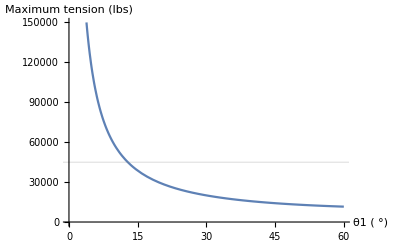

```mathematica
Plot[maxTension[var],{var,0,60},PlotRange->{0,150000},GridLines->{{45000}},AxesLabel->{"θ1 ( °)","Maximum tension (lbs)"}]
```

Of course, this allows us to Solve for that intersection point...

```mathematica
optimum=FindRoot[maxTension[var]==45000,{var,10}]
```

{var→12.8396}

This means the entire structure can be optimized to a vertical spread between wall mountpoints of

```mathematica
Sin[(var/.optimum) Degree]Quantity[, "Feet"]
```

0.222222 ft

Not bad.

## Misc

```mathematica
NSolve[x=={1,2},x,Vectors[2]]
```

NSolve::bdomv: Warning: Vectors[2,Complexes] is not a valid domain specification. Assuming it is a variable to eliminate.

{}

```mathematica
Array
```

```mathematica
soleq1,soleq2,soleq3,xval,yval,zval
```

```mathematica
CoefficientArrays[]
```

```mathematica
elim3[x+y+z==6,x+y+z==6,x+y+z==6]
```

Part::partw: Part 1 of {} does not exist.

{6-z-{}⟦1,2⟧,{}⟦1,2⟧,z}

```mathematica
soleq1
```

{x→6-y-z}

```mathematica
soleq2
```

{}

```mathematica
(x+y+z==6)/.soleq1
```

True

```mathematica
LUDecomposition[{{0,1},{1,0}}]
```

{{{1,0},{0,1}},{2,1},0}

```mathematica
RowReduce[({{a, b, 1, 0}, {c, d, 0, 1}})]
```

{{1,0,d/(-b c+a d),b/(b c-a d)},{0,1,c/(b c-a d),a/(-b c+a d)}}

```mathematica
Partition[%,{2,2}]
```

{{{{1,0},{0,1}},{{d/(-b c+a d),b/(b c-a d)},{c/(b c-a d),a/(-b c+a d)}}}}

```mathematica
%[[1,2]]
```

{{d/(-b c+a d),b/(b c-a d)},{c/(b c-a d),a/(-b c+a d)}}

```mathematica
val=%
```

{{d/(-b c+a d),b/(b c-a d)},{c/(b c-a d),a/(-b c+a d)}}

```mathematica
FullSimplify[Inverse@val]
```

{{a,b},{c,d}}

```mathematica
HoldForm@Inverse@IdentityMatrix[5]//Transpose//TraditionalForm
```

Transpose[(IdentityMatrix[5])]

```mathematica
Partition[StringSplit@TextRecognize[-Graphics-],6]//MatrixForm
```

(- | sin30 | - | cos30 | cos | 30
sin | 30 | 0 | 0 | 0 | 0
1 | 0 | fl | 0 | - | sin60
cos | 60 | 0 | 0 | - | cos)

```mathematica
Head[5]==Integer
```

True

```mathematica
List==Inverse
```

List==Inverse

```mathematica
(Real===Integer)
```

False

```mathematica
N[Sin[Pi/3],800]
```

0.86602540378443864676372317075293618347140262690519031402790348972596650845440001854057309337862428783781307070770335151498497254749947623940582775604718682426404661595115279103398741005054233746163250765617163345166144332533612733446091898561352356583018393079400952499326868992969473382517375328802537830917406480305047380109359516254157291476197991649889491225414435723191645867361208199229392769883397903190917683305542158689044718915805104415276245083501176035557214434799547818289854358424903644974664824214151039320430199436934876879115865891569799649150391935143852695668478165605185363200962455338411559964418782057071100837137605118649713541552994922973799383214444889807391897919511442742645178801692640403219098617233052984486143643263207691133234921001059774207763922059064326725351759583